```mathematica
1+1
```

2

```mathematica
2 3
```

```mathematica
%^3
```

216

```mathematica
2 5
```

```mathematica
10^2
```

100

```mathematica
1/2+1/3
```

5/6

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

```mathematica
Exp[2]
```

```mathematica
(ⅇ^2)^2
```

```mathematica
ⅇ^4
```

```mathematica
N[ⅇ^4,15]
```

54.5981500331442

```mathematica
Exp[2]
```

ⅇ^2

```mathematica
N[%,15]
```

7.38905609893065

```mathematica
∑_(n=1)^∞ 1/(n n)
```

π^2/6

```mathematica
∑_(n=1)^∞ 1/n^3
```

Zeta[3]

```mathematica
2x+y-x-3y
```

x-2 y

```mathematica
Expand[(2x-1)^6]
```

```mathematica
1-12 x+60 x^2-160 x^3+240 x^4-192 x^5+64 x^6
%//TraditionalForm
```

1-12 x+60 x^2-160 x^3+240 x^4-192 x^5+64 x^6

64 x^6-192 x^5+240 x^4-160 x^3+60 x^2-12 x+1

```mathematica
Factor[%]
```

(-1+2 x)^6

```mathematica
f = (2x-1)^6
```

(-1+2 x)^6

```mathematica
x=3
```

3

```mathematica
f
```

15625

```mathematica
Clear[f] //注意大小写
```

```mathematica
Clear[x]
```

```mathematica
f
```

f

```mathematica
f[x_]:=(2x-1)^6
```

```mathematica
f[3]
```

15625

```mathematica
f[2]
```

729

```mathematica
Manipulate[Factor[x^n-1],{n,0,100,1}]
```

```mathematica
Solve[x^3-4x==0,x]
```

{{x→-2},{x→0},{x→2}}

```mathematica
Solve[{x+y==1,2x-5y==3},{x,y}]
```

{{x→8/7,y→-1/7}}

```mathematica
FindRoot[Cos[x]-x==0,{x,1}]
```

{x→0.739085}

FindRoot::nlnum: {x} = {1.}において，関数の値{-1. + cos[1.]}は次元{1}の数値のリストではありません．

FindRoot[cos[x]-x==0,{x,1}]

```mathematica
D[(x^2y^3), y]
```

```mathematica
3 x^2 y^2
D[x^2y^3,y]
```

3 x^2 y^2

3 x^2 y^2

```mathematica
∫1/(1+x^3)ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Partitions::shdw: 複数のコンテキスト{Combinatorica`,Global`}においてシンボルPartitionsが使われています．コンテキストCombinatorica`の定義は他の定義で隠れてしまう可能性があります．

```mathematica
Partitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

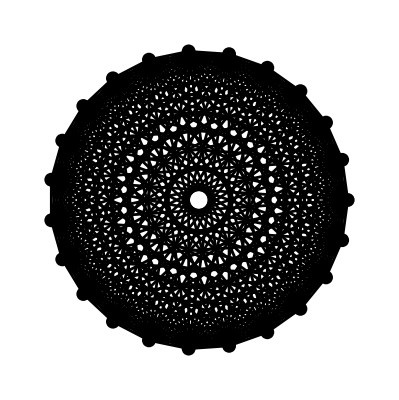

```mathematica
ShowGraph[CompleteGraph[23]]
```

```mathematica
a=Range[5]
```

{1,2,3,4,5}

```mathematica
b=Range[2,10,2]
```

{2,4,6,8,10}

```mathematica
c=Table[n^2,{n,1,5}]
```

{1,4,9,16,25}

```mathematica
a+b
```

{3,6,9,12,15}

```mathematica
a b
```

{2,8,18,32,50}

```mathematica
a/b
```

{1/2,1/2,1/2,1/2,1/2}

```mathematica
b^a
```

{2,16,216,4096,100000}

```mathematica
a.b //内积
```

110

```mathematica
p={0.2,0.3,0.5}
```

{0.2,0.3,0.5}

```mathematica
Log2[p]
```

{-2.32193,-1.73697,-1.}

```mathematica
-p.Log2[p]
```

1.48548

```mathematica
Attributes[Log]//解释函数
```

{Listable,NumericFunction,Protected}

```mathematica
m={{1,1,-2},{1,-2,1},{3,-2,-1}}
```

{{1,1,-2},{1,-2,1},{3,-2,-1}}

```mathematica
%//MatrixForm
```

(1 | 1 | -2
1 | -2 | 1
3 | -2 | -1)

```mathematica
Eigenvalues[m]
```

{-1+ⅈ √5,-1-ⅈ √5,0}

```mathematica
Eigenvectors[m]
```

{{-(-3 ⅈ-√5)/(-ⅈ+3 √5),-(3 ⅈ-√5)/(-ⅈ+3 √5),1},{-(3 ⅈ-√5)/(ⅈ+3 √5),-(-3 ⅈ-√5)/(ⅈ+3 √5),1},{1,1,1}}

```mathematica
For[i=1,i≤4,i++,Print[i^2]]
```

1

4

9

16

```mathematica
BernoulliB[10]
```

5/66

```mathematica
Table[BernoulliB[i],{i,0,10}]
```

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}